```mathematica
SetDirectory[NotebookDirectory[]];
Get["PhLib.wl"];
```

```mathematica
Catch[
file="ATERRAMENTO\\0.fasor";
res = PhLib`ReadPhasor[file];
(* PhLib`PolarDiagram[PhLib`scale[res[[1]]], "1381"] *)
]
```

```mathematica
comp2 = {{"A138","A230"}, {"B138","B230"}, {"C138","C230"}, 
{"AIA1381","AIA2301"},{"AIB1381","AIB2301"},{"AIC1381","AIC2301"} ,
{"AIA1382","AIA2302"},{"AIB1382","AIB2302"},{"AIC1382","AIC2302"}
};

comp = {
{"A138","AIA1381"}, {"B138","AIB1381"}, {"C138","AIC1381"}, 
{"A138","AIA1382"}, {"B138","AIB1382"}, {"C138","AIC1382"} ,
{"A230","AIA2301"}, {"B138","AIB2301"}, {"C138","AIC2301"},
{"A230","AIA2302"}, {"B138","AIB2302"}, {"C138","AIC2302"}
};

comp3 = {
{"A138","IA1381"}, {"B138","IB1381"}, {"C138","IC1381"}, 
{"A138","IA1382"}, {"B138","IB1382"}, {"C138","IC1382"} ,
{"A230","IA2301"}, {"B138","IB2301"}, {"C138","IC2301"},
{"A230","IA2302"}, {"B138","IB2302"}, {"C138","IC2302"}
};

i = 0;
files = {};
While[ i< 1,
file = FileNameJoin[{"ATERRAMENTO",ToString[i] <> ".fasor"}];
res = PhLib`ReadPhasor[file];

teste =Abs[res[[All,#[[2]]]] - res[[All,#[[1]] ]]] &/@ comp;
If[ Max[teste] > 1, AppendTo[files,file]];
++i;
];
```

```mathematica
rel = {};
Do[
res  = PhLib`ReadPhasor[f];
Do[ 
teste= res[[All,c[[2]]]] - res[[All,c[[1]] ]];
teste = PhLib`toang /@ teste;
If[ Max[teste] > 1, 
i = Position[teste,x_ /; x > 1][[1,1]];
AppendTo[rel, 
{f,c}->Table[{res[[j,c[[1]]]],res[[j, c[[2]]]], teste[[j]]},{j,{Max[i-1,1],i}}]
]
];
 ,{c, comp3}]
,{f,files}];
```

```mathematica
rel //TableForm
```

{}

```mathematica
file="BATEIAS_04-06\\0.fasor";
res = PhLib`ReadPhasor[file];
ds = PhLib`ReadHeadPhasors[file, 2, "Week"];
```

```mathematica
Compare[F1_, F2_, F3_] := 
Column[{
StringForm[ " `` vs `` = `` ", 
F1,F3, NumberForm[MedianDeviation[ PhLib`toang /@ ( ds[[All,F1]]-ds[[All,F3]] )],{3,4}]
],
StringForm[ " `` vs `` = `` ",
F2,F3, NumberForm[MedianDeviation[ PhLib`toang /@ ( ds[[All,F2]]-ds[[All,F3]] )],{3,4}]
],
StringForm[ " `` vs `` = `` ",
F1,F2, NumberForm[ MedianDeviation[ PhLib`toang /@ ( ds[[All,F1]]-ds[[All,F2]] )],{3,4}]
],
StringForm[ " `` vs `` ref `` ``",F1,F2,F3, 
NumberForm[Correlation[ 
PhLib`toang /@ ( ds[[All,F1]]-ds[[All,F3]] ),
PhLib`toang /@ ( ds[[All,F2]]-ds[[All,F3]] )],{3,4}]
],
StringForm[ " `` vs `` ref `` ``",F1,F3,F2, 
NumberForm[Correlation[ 
PhLib`toang /@ ( ds[[All,F1]]-ds[[All,F2]] ),
PhLib`toang /@ ( ds[[All,F3]]-ds[[All,F2]] )],{3,4}]
],
StringForm[ " `` vs `` ref `` ``",F2,F3,F1, 
NumberForm[Correlation[ 
PhLib`toang /@ ( ds[[All,F2]]-ds[[All,F1]] ),
PhLib`toang /@ ( ds[[All,F3]]-ds[[All,F1]] )],{3,4}]
]
}]
```

```mathematica
Grid[{
{Compare["IA1381","IB1381","IC1381"],
Compare["IA1382","IB1382","IC1382"]},
{Compare["IA2301","IB2301","IC2301"],
Compare["IA2302","IB2302","IC2302"]},
{Compare["A138","B138","C138"],
Compare["A230","B230","C230"]},
{Compare["IA1381","IA1382","A138"],
Compare["IA2301","IA2302","A230"]},
{Compare["IB1381","IB1382","B138"],
Compare["IB2301","IB2302","B230"]},
{Compare["IC1381","IC1382","C138"],
Compare["IC2301","IC2302","C230"]}
}, Frame->All]
```

IA1381 vs IC1381 = 0.0802 
 IB1381 vs IC1381 = 0.0328 
 IA1381 vs IB1381 = 0.0609 
 IA1381 vs IB1381 ref IC1381 0.6660
 IA1381 vs IC1381 ref IB1381 -0.3170
 IB1381 vs IC1381 ref IA1381 0.9180 |  IA1382 vs IC1382 = 0.0534 
 IB1382 vs IC1382 = 0.0564 
 IA1382 vs IB1382 = 0.0245 
 IA1382 vs IB1382 ref IC1382 0.8950
 IA1382 vs IC1382 ref IB1382 0.3590
 IB1382 vs IC1382 ref IA1382 0.0952
 IA2301 vs IC2301 = 0.0594 
 IB2301 vs IC2301 = 0.0519 
 IA2301 vs IB2301 = 0.0189 
 IA2301 vs IB2301 ref IC2301 0.9300
 IA2301 vs IC2301 ref IB2301 -0.1410
 IB2301 vs IC2301 ref IA2301 0.4940 |  IA2302 vs IC2302 = 0.0424 
 IB2302 vs IC2302 = 0.0418 
 IA2302 vs IB2302 = 0.0200 
 IA2302 vs IB2302 ref IC2302 0.8340
 IA2302 vs IC2302 ref IB2302 0.1960
 IB2302 vs IC2302 ref IA2302 0.3780
 A138 vs C138 = 0.0251 
 B138 vs C138 = 0.0299 
 A138 vs B138 = 0.0209 
 A138 vs B138 ref C138 0.6410
 A138 vs C138 ref B138 0.4780
 B138 vs C138 ref A138 0.3680 |  A230 vs C230 = 0.0242 
 B230 vs C230 = 0.0311 
 A230 vs B230 = 0.0239 
 A230 vs B230 ref C230 0.5700
 A230 vs C230 ref B230 0.5350
 B230 vs C230 ref A230 0.3900
 IA1381 vs A138 = 0.0900 
 IA1382 vs A138 = 0.0666 
 IA1381 vs IA1382 = 0.0250 
 IA1381 vs IA1382 ref A138 0.9630
 IA1381 vs A138 ref IA1382 -0.1280
 IA1382 vs A138 ref IA1381 -0.0004 |  IA2301 vs A230 = 0.0221 
 IA2302 vs A230 = 0.0221 
 IA2301 vs IA2302 = 0.0061 
 IA2301 vs IA2302 ref A230 0.9630
 IA2301 vs A230 ref IA2302 -0.1280
 IA2302 vs A230 ref IA2301 -0.0003
 IB1381 vs B138 = 0.0408 
 IB1382 vs B138 = 0.0729 
 IB1381 vs IB1382 = 0.0357 
 IB1381 vs IB1382 ref B138 0.9630
 IB1381 vs B138 ref IB1382 0.0056
 IB1382 vs B138 ref IB1381 0.0001 |  IB2301 vs B230 = 0.0154 
 IB2302 vs B230 = 0.0142 
 IB2301 vs IB2302 = 0.0089 
 IB2301 vs IB2302 ref B230 0.9630
 IB2301 vs B230 ref IB2302 -0.1280
 IB2302 vs B230 ref IB2301 -0.0004
 IC1381 vs C138 = 0.0115 
 IC1382 vs C138 = 0.0148 
 IC1381 vs IC1382 = 0.0062 
 IC1381 vs IC1382 ref C138 0.9630
 IC1381 vs C138 ref IC1382 -0.1280
 IC1382 vs C138 ref IC1381 -0.0004 |  IC2301 vs C230 = 0.0293 
 IC2302 vs C230 = 0.0135 
 IC2301 vs IC2302 = 0.0185 
 IC2301 vs IC2302 ref C230 0.9630
 IC2301 vs C230 ref IC2302 -0.1270
 IC2302 vs C230 ref IC2301 -0.0005

```mathematica
pf[f_,t_] := (# - Mean[#]) & [ PhLib`toang /@ (ds[[All,"I" <> f <> t]]-ds[[All,f]]) ];
```

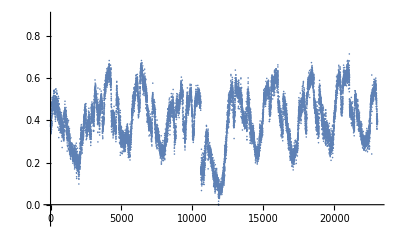
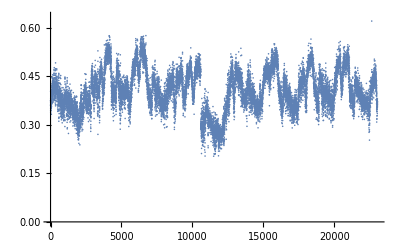
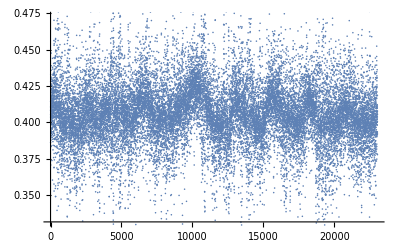
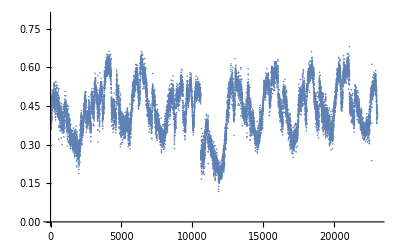
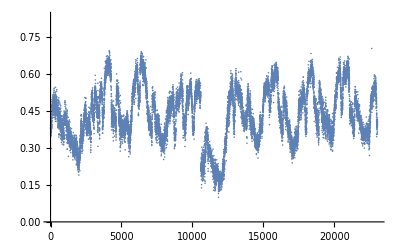
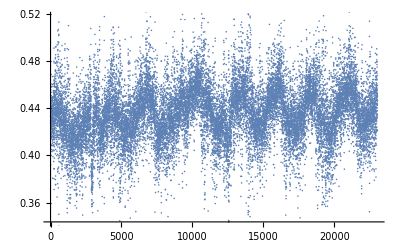
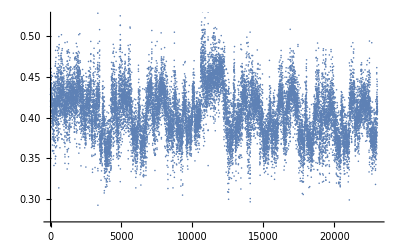
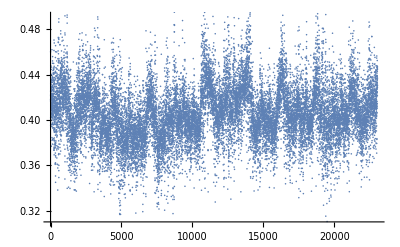
-Graphics-X1 - FASE A | -Graphics-X1 - FASE B | -Graphics-X1 - FASE C
-Graphics-X2 - FASE A | -Graphics-X2 - FASE B | -Graphics-X2 - FASE C
-Graphics-H1 - FASE A | -Graphics-H1 - FASE B | -Graphics-H1 - FASE C
-Graphics-H2 - FASE A | -Graphics-H2 - FASE B | -Graphics-H2 - FASE C

```mathematica
Grid[{
{Labeled[ListPlot[ pf["A138","1"], PlotRange->Automatic], "X1 - FASE A"],
Labeled[ListPlot[pf["B138","1"], PlotRange->Automatic], "X1 - FASE B"],
Labeled[ListPlot[pf["C138","1"], PlotRange->Automatic], "X1 - FASE C"]},
{Labeled[ListPlot[pf["A138","2"], PlotRange->Automatic], "X2 - FASE A"],
Labeled[ListPlot[pf["B138","2"], PlotRange->Automatic], "X2 - FASE B"],
Labeled[ListPlot[pf["C138","2"], PlotRange->Automatic], "X2 - FASE C"]},
{Labeled[ListPlot[pf["A230","1"], PlotRange->Automatic], "H1 - FASE A"],
Labeled[ListPlot[pf["B230","1"], PlotRange->Automatic], "H1 - FASE B"],
Labeled[ListPlot[pf["C230","1"], PlotRange->Automatic], "H1 - FASE C"]},
{Labeled[ListPlot[pf["A230","2"], PlotRange->Automatic], "H2 - FASE A"],
Labeled[ListPlot[pf["B230","2"], PlotRange->Automatic], "H2 - FASE B"],
Labeled[ListPlot[pf["C230","2"], PlotRange->Automatic], "H2 - FASE C"]}
}]
```

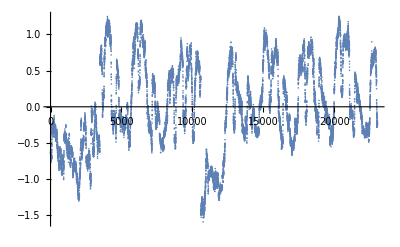

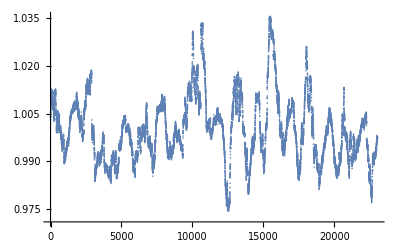

```mathematica
fang[res_, offset_] := Table[  (180/Pi)*( r["data"][[-1,1]] - offset), {r,res}];
famp[res_, offset_] := Table[   r["data"][[-1,2]] / offset, {r,res}];
res = {};
Do [ AppendTo[res, PhLib`PolarData[PhLib`scale[d],"2301"] ], {d,ds}];
ListPlot[fang[res, Mean@res[[All,"data"]][[All,-1,1]]]]
ListPlot[famp[res, Mean@res[[All,"data"]][[All,-1,2]]]]
```

{}

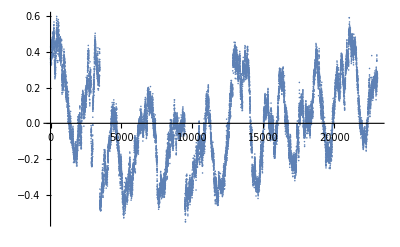

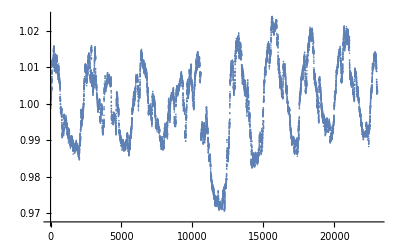

```mathematica
res = {}
Do [ AppendTo[res, PhLib`PolarData[PhLib`scale[d],"2302"] ], {d,ds}];
ListPlot[fang[res, Mean@res[[All,"data"]][[All,-1,1]]]]
ListPlot[famp[res, Mean@res[[All,"data"]][[All,-1,2]]]]
```

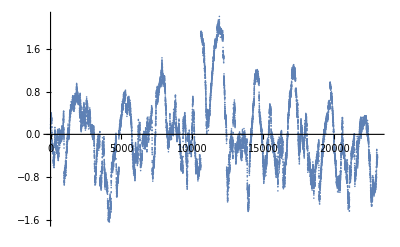

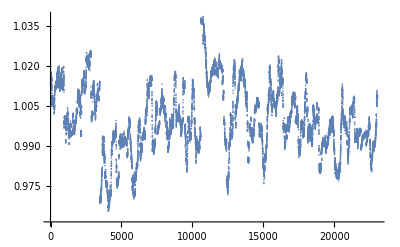

```mathematica
res = {};
Do [ AppendTo[res, PhLib`PolarData[PhLib`scale[d],"1381"] ], {d,ds}];
ListPlot[fang[res, Mean@res[[All,"data"]][[All,-1,1]]]]
ListPlot[famp[res, Mean@res[[All,"data"]][[All,-1,2]]]]
```

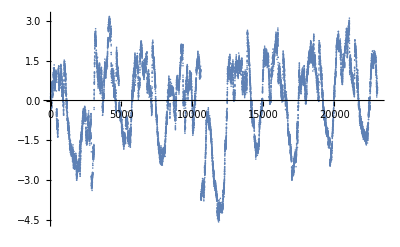

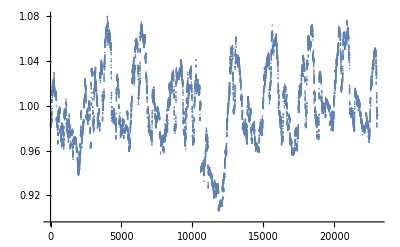

```mathematica
res = {};
Do [ AppendTo[res, PhLib`PolarData[PhLib`scale[d],"1382"] ], {d,ds}];
ListPlot[fang[res, Mean@res[[All,"data"]][[All,-1,1]]]]
ListPlot[famp[res, Mean@res[[All,"data"]][[All,-1,2]]]]
```

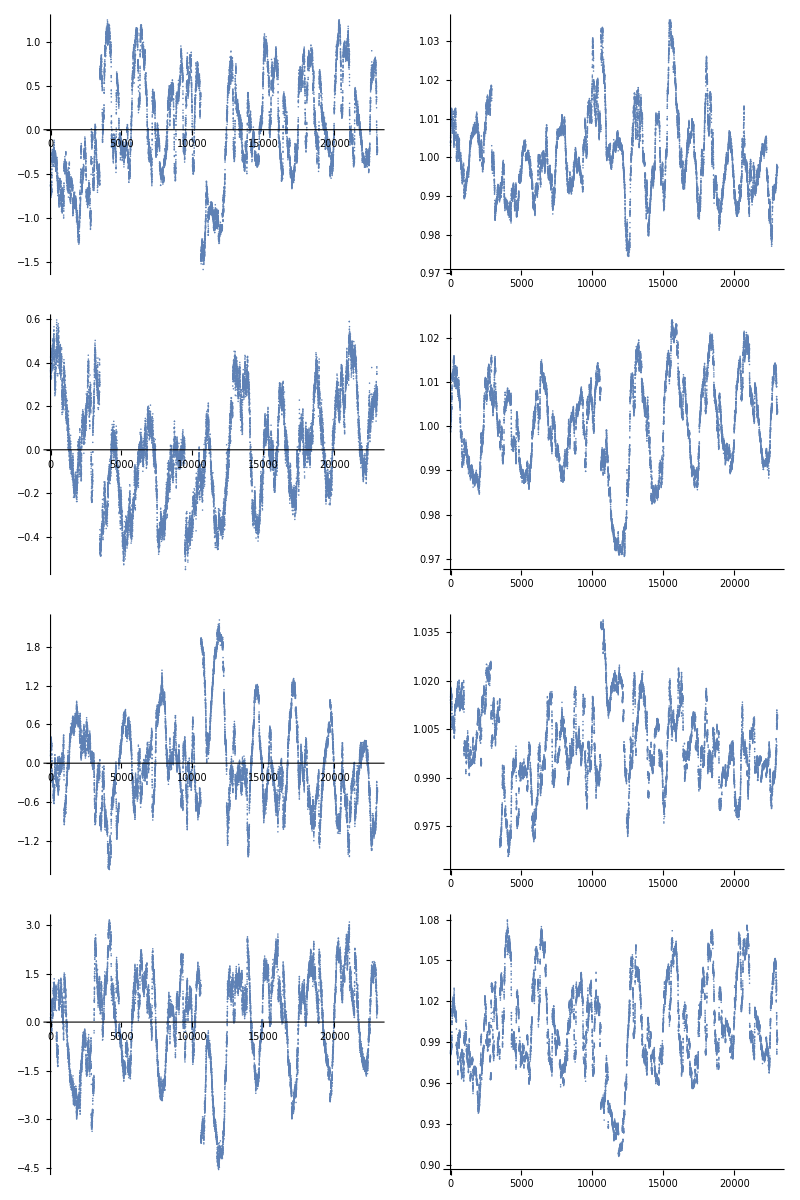

```mathematica
Grid[{{Out[779],Out[780]},{Out[771],Out[772]},{Out[754],Out[755]},{Out[764],Out[765]}}]
```